# Kelvin Problem in 2-d plane strain

```mathematica
x = xo - xs
y = yo - ys
C0 = 1/ (4 * Pi *(1-nu))
r = Sqrt[x^2 + y^2]
g = -C0 * Log[r]
gx = -C0*x/r^2
gy = -C0*y/r^2
ux = fx/(2*mu)*((3-4*nu)*g - x*gx) + fy/(2*mu)*(-y*gx)
uy = fx/(2*mu)*(-x*gy) + fy/(2*mu)*((3-4*nu)*g -y*gy)
```

xo-xs

yo-ys

1/(4 (1-nu) π)

√((xo-xs)^2+(yo-ys)^2)

-Log[√((xo-xs)^2+(yo-ys)^2)]/(4 (1-nu) π)

-(xo-xs)/(4 (1-nu) π ((xo-xs)^2+(yo-ys)^2))

-(yo-ys)/(4 (1-nu) π ((xo-xs)^2+(yo-ys)^2))

-(fy (xo-xs) (-yo+ys))/(8 mu (1-nu) π ((xo-xs)^2+(yo-ys)^2))+(fx ((xo-xs)^2/(4 (1-nu) π ((xo-xs)^2+(yo-ys)^2))-((3-4 nu) Log[√((xo-xs)^2+(yo-ys)^2)])/(4 (1-nu) π)))/(2 mu)

-(fx (-xo+xs) (yo-ys))/(8 mu (1-nu) π ((xo-xs)^2+(yo-ys)^2))+(fy ((yo-ys)^2/(4 (1-nu) π ((xo-xs)^2+(yo-ys)^2))-((3-4 nu) Log[√((xo-xs)^2+(yo-ys)^2)])/(4 (1-nu) π)))/(2 mu)

```mathematica
uxmod = ReplaceAll[ux,{ys->0,yo->0}]
uymod = ReplaceAll[uy,{ys->0,yo->0}]
uxint = Integrate[uxmod,{xs,-1,1}]
uyint = Integrate[uymod,{xs,-1,1}]
```

(fx (1/(4 (1-nu) π)-((3-4 nu) Log[√((xo-xs)^2)])/(4 (1-nu) π)))/(2 mu)

-(fy (3-4 nu) Log[√((xo-xs)^2)])/(8 mu (1-nu) π)

ConditionalExpression[-(fx (4+(-3+4 nu) (-4-(-1+xo) Log[(-1+xo)^2]+(1+xo) Log[(1+xo)^2])))/(16 mu (-1+nu) π), xo∈ℝ||Re[xo]≥1||Re[xo]≤-1]

ConditionalExpression[(fy (-3+4 nu) (4+(-1+xo) Log[(-1+xo)^2]-(1+xo) Log[(1+xo)^2]))/(16 mu (-1+nu) π), xo∈ℝ||Re[xo]≥1||Re[xo]≤-1]

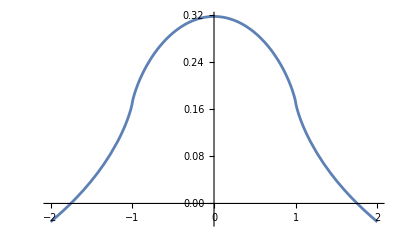

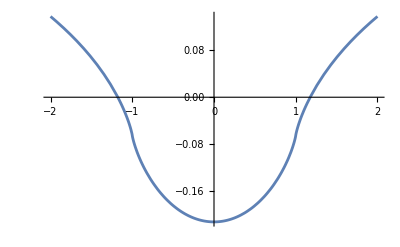

```mathematica
Plot[ ReplaceAll[uxint,{fx -> 1, mu->1,nu->0.25}],{xo,-2,2}]
Plot[ ReplaceAll[uyint,{fy -> -1, mu->1,nu->0.25}],{xo,-2,2}]
```

```mathematica
uxmod2 = ReplaceAll[ux, {fy->0, mu->1,nu->0.25}]
uxint2 = Integrate[uxmod2,{xs,-1,1},{ys,-1,1}]
```

0.+1/2 fx ((0.106103 (xo-xs)^2)/((xo-xs)^2+(yo-ys)^2)-0.212207 Log[√((xo-xs)^2+(yo-ys)^2)])

$Aborted

Infinity::indet: Indeterminate expression (0.+0. ⅈ) (-∞) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

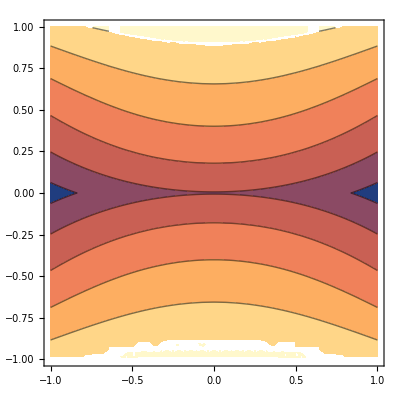

```mathematica
Plot[ReplaceAll[uxint2,{fx -> 1,yo->0}],{xo,-1,1}]
ContourPlot[ReplaceAll[uxint2,{fx -> 1}],{xo,-1,1},{yo,-1,1}]
```